# GDT ECH with linear Slab Profiles cold electrons, 20ev ions

## Open Additional files:

## Get dispersion routines by evaluating Disper.nb Get plotting and printing routines by evaluating PlotPack.nb Set Parameters by opening a Parameter Window Note: Slab profile models defined in initialization cells at the bottom of this notebook.

## First Do Cold Plasma

### Plot Real and Imaginary parts of nx from 2nd order warm plasma dispersion relation (i.e. E_‖≡0)

```mathematica
nPerpCold[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
     ColdDis0[freq,ne,b,nz,etaList]]
nt=Table[{x,nPerpCold[x]},{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexListPlot[nt,"x (m)","nx"]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

-Graphics-

dataSet=GDT Kinetic Alfven 10MHz

xProfileMin=1.×10^19

xProfileMax=3.×10^19

nXmin=1.×10^19

nXmax=3.×10^19

BXmin=1.2

BXmax=1.2

freq=7.5

nz=127.324

etaList={0.,1.,0.,0.,0.}

xmin=1.×10^19

xmax=3.×10^19

### Plot Real and Imaginary parts of nx from 4nd order cold plasma dispersion relation (i.e. fast and slow)

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		ColdDis2FS[freq,ne,b,nz,etaList]]
nt2FS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=ComplexListPlot[nF,"x (m)","nx"];
g2=ComplexListPlot[nS,"x (m)","nx"];
Show[{g1,g2},PlotRange->{0.,1000.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmin}];
```

-Graphics-

dataSet=GDT Kinetic Alfven 10MHz

xProfileMin=1.×10^19

xProfileMax=3.×10^19

nXmin=1.×10^19

nXmax=3.×10^19

BXmin=1.2

BXmax=1.2

freq=7.5

nz=127.324

etaList={0.,1.,0.,0.,0.}

xmin=1.×10^19

xmin=1.×10^19

## Now Warm Plasma Stuff

### Plot Real and Imaginary parts of nx from 6th order warm plasma dispersion relation (expanded to 2nd order in k_⌊ρ)

```mathematica
nPerpWarm6[x_]:=Module[{ne,te,b,x0,TL},
		x0=x;
     ne=nprof[x0];
b=bprof[x0];
	  TL=tprof[x0] *TList;
	  WarmDis6[freq,ne,b,nz,etaList,TL]]
```

#### Compare to cold plasma roots

```mathematica
nPerp2FS[xmin]
nPerpWarm6[xmin]
```

{0.+54.7543 ⅈ,3838.1}

{0.+54.4523 ⅈ,4325.34,11049.2,0.-54.4523 ⅈ,-4325.34,-11049.2}

Gets a root near the cutoff fast wave branch, slow wave different but there.  Try closer to resonance.

```mathematica
nPerp2FS[xmin/4.]
nPerpWarm6[xmin/4.]
```

{0.+118.424 ⅈ,5048.18}

{0.+118.408 ⅈ,5786.15,10868.4,0.-118.408 ⅈ,-5786.15,-10868.4}

Slow wave actually closer

```mathematica
nPerp2FS[0.]
nPerpWarm6[0.]
```

{0.+127.32 ⅈ,0.+127.32 ⅈ}

{0.+127.32 ⅈ,0.+127.32 ⅈ,0.-127.32 ⅈ,0.-127.32 ⅈ}

#### Plot kx profile for 6 th order system

```mathematica
nxwarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
roots=rootSort[nxwarm];
rootsRe=Table[Flatten[{roots[[i]][[1]],Table[Re[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

rootsIm=Table[Flatten[{roots[[i]][[1]],Table[Im[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

g6=ComplexVectorListPlot[roots,"x (m)","nx"];
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TeXmin,TeXmax,TList, modelList,xmin,xmax}];
Show[g6,PlotRange->All]
Show[g6,PlotRange->{-2000.,2000.}]
ComplexVectorListPlot[rootsRe, "x", "Re[kx]",PlotRange->{-2000.,2000.}]
ComplexVectorListPlot[rootsIm, "x", "Im[kx]",PlotRange->{-2000.,2000.}]
```

dataSet=GDT Kinetic Alfven 10MHz

xProfileMin=1.×10^19

xProfileMax=3.×10^19

nXmin=1.×10^19

nXmax=3.×10^19

BXmin=1.2

BXmax=1.2

freq=7.5

nz=127.324

etaList={0.,1.,0.,0.,0.}

TeXmin=0.02

TeXmax=0.02

TList={0.,0.,1.,0.,0.,0.}

modelList={1,1,0,0,0,0}

xmin=1.×10^19

xmax=3.×10^19

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

Looks plausible but the numbers aren' t close to cold plasma even at 5 ev.

## Now Try with Hot Plasma Dispersion using root finder

```mathematica
nPerpHot[x_,nxGuess_]:=Module[{ne,b,x0,TL,nx0},
		x0=x;
nx0=nxGuess;
     ne=nprof[x0];
b=bprof[x0];
     TL=tprof[x0]*TList;
rootRule=FindRoot[DisFuncGeneral[freq,ne,b,nz,nx,etaList,TL,nminList,nmaxList,modelList],{nx,nx0}, MaxIterations->30];
nx/.rootRule]
```

### First try root finding on warm plasma dispersion rel (model = 1)

```mathematica
modelList =Table[1,{i,1,6}];
```

#### Compare to cold plasma and 6th order system roots

```mathematica
nPerp2FS[xmin]
nPerpWarm6[xmin]
nPerpHot[xmin,nPerp2FS[xmin][[1]]]
nPerpHot[xmin,nPerp2FS[xmin][[2]]]
nPerpHot[xmin,nPerpWarm6[xmin][[1]]]
nPerpHot[xmin,nPerpWarm6[xmin][[2]]]
nPerpHot[xmin,nPerpWarm6[xmin][[3]]]
```

{0.+54.7543 ⅈ,3838.1}

{0.+54.4523 ⅈ,4325.34,11049.2,0.-54.4523 ⅈ,-4325.34,-11049.2}

2.76081×10^-58+54.4523 ⅈ

4325.34-5.98199×10^-57 ⅈ

2.76081×10^-58+54.4523 ⅈ

4325.34

11049.2

Solutions from FindRoot (nPerpHot) agree with solutions from NSolve (nPerpWarm)

#### Look closer to resonance

```mathematica
nPerp2FS[xmin/4.]
nPerpWarm6[xmin/4.]
nPerpHot[xmin/4.,nPerpWarm6[xmin/4.][[1]]]
nPerpHot[xmin/4.,nPerpWarm6[xmin/4.][[2]]]
nPerpHot[xmin/4.,nPerpWarm6[xmin/4.][[3]]]
```

{0.+118.424 ⅈ,5048.18}

{0.+118.408 ⅈ,5786.15,10868.4,0.-118.408 ⅈ,-5786.15,-10868.4}

1.21921×10^-59+118.408 ⅈ

5786.15

10868.4-1.95346×10^-57 ⅈ

#### Plot nx profile from root finder but still with 6th order system (model = 1)

```mathematica
modelList =Table[1,{i,1,6}];(* Set model *)
```

```mathematica
nxhot[iRoot_]:=Module[{iRoot0,nxWarm,rootsWarm,nxH,x0,ne,b,t,TL},
nxWarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
iRoot0=iRoot;
rootsWarm=rootSort[nxWarm];
nxH=Table[0.,{i,1,nPoints}];
Do[
(x0=xmin+(i-1)(xmax-xmin)/(nPoints-1);
nxGuess=rootsWarm[[i]][[iRoot0+1]];
(*Print["x0 = ", x0,"  nxGuess= ",nxGuess];*)
nxH[[i]]={x0,nPerpHot[x0,nxGuess]};),{i,1,nPoints}];
nxH];
g7=ComplexVectorListPlot[nxhot[1],"x (m)","nx"];g8=ComplexVectorListPlot[nxhot[2],"x (m)","nx"];g9=ComplexVectorListPlot[nxhot[3],"x (m)","nx"];g10=ComplexVectorListPlot[nxhot[4],"x (m)","nx"];
g11=ComplexVectorListPlot[nxhot[5],"x (m)","nx"];
g12=ComplexVectorListPlot[nxhot[6],"x (m)","nx"];
Show[{g7,g8,g10,g11},PlotRange->All]
Show[{g7,g8,g10,g11},PlotRange->{-1000.,1000.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TeXmin,TeXmax,TList,modelList,xmin,xmax}];
```

-Graphics-

-Graphics-

dataSet=GDT Kinetic Alfven 10MHz

xProfileMin=1.×10^19

xProfileMax=3.×10^19

nXmin=1.×10^19

nXmax=3.×10^19

BXmin=1.2

BXmax=1.2

freq=7.5

nz=127.324

etaList={0.,1.,0.,0.,0.}

TeXmin=0.02

TeXmax=0.02

TList={0.,0.,1.,0.,0.,0.}

modelList={1,1,1,1,1,1}

xmin=1.×10^19

xmax=3.×10^19

#### Now try with hot plasma (model = 2) for all species. Can I find the warm plasma roots with the full dispersion relation?

Change model to 2

```mathematica
modelList =Table[2,{i,1,6}];
```

```mathematica
xPoint=xmin;
nPerp2FS[xPoint]
guesses=nPerpWarm6[xPoint]  (* Warm plasma roots at x=0  *)
```

{0.+54.7543 ⅈ,3838.1}

{0.+54.4523 ⅈ,4325.34,11049.2,0.-54.4523 ⅈ,-4325.34,-11049.2}

```mathematica
{nPerpHot[xPoint,guesses[[1]]],
nPerpHot[xPoint,guesses[[2]]],
nPerpHot[xPoint,guesses[[3]]],
nPerpHot[xPoint,guesses[[4]]],
nPerpHot[xPoint,guesses[[5]]],
nPerpHot[xPoint,guesses[[6]]]}
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TeXmin,TeXmax,TList,modelList,nminList,nmaxList,xmin,xmax}];
```

{2.76081×10^-58+54.4523 ⅈ,4276.55-4.34809×10^-57 ⅈ,4276.55-4.86021×10^-57 ⅈ,-2.76081×10^-58-54.4523 ⅈ,-4276.55+4.34809×10^-57 ⅈ,-4276.55+4.86021×10^-57 ⅈ}

dataSet=GDT Kinetic Alfven 10MHz

xProfileMin=1.×10^19

xProfileMax=3.×10^19

nXmin=1.×10^19

nXmax=3.×10^19

BXmin=1.2

BXmax=1.2

freq=7.5

nz=127.324

etaList={0.,1.,0.,0.,0.}

TeXmin=0.02

TeXmax=0.02

TList={0.,0.,1.,0.,0.,0.}

modelList={2,2,2,2,2,2}

nminList={-1,-2,-2,-2,-2,-2}

nmaxList={1,2,2,2,2,2}

xmin=1.×10^19

xmax=3.×10^19

xmax=0.04

Hot plasma root finder gets 2 of the 6th order roots.  Try initializing with cold plasma roots

```mathematica
{nPerpHot[xPoint,nPerp2FS[xPoint][[1]]],nPerpHot[xPoint,nPerp2FS[xPoint][[2]]]}
```

{2.76081×10^-58+54.4523 ⅈ,4276.55-5.7609×10^-57 ⅈ}

### Plot hot plasma vs x

```mathematica
g7=ComplexVectorListPlot[nxhot[1],"x (m)","nx"];g8=ComplexVectorListPlot[nxhot[2],"x (m)","nx"];g9=ComplexVectorListPlot[nxhot[3],"x (m)","nx"];g10=ComplexVectorListPlot[nxhot[4],"x (m)","nx"];
g11=ComplexVectorListPlot[nxhot[5],"x (m)","nx"];
g12=ComplexVectorListPlot[nxhot[6],"x (m)","nx"];
Show[{g7,g8,g9,g10,g11,g12},PlotRange->All,AxesOrigin->{0.,0.}]
Show[{g7,g8,g9,g10,g11,g12},PlotRange->{-1000.,1000.},AxesOrigin->{0.,0.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TeXmin,TeXmax,TList,modelList,nminList,nmaxList,xmin,xmax}];
```

-Graphics-

-Graphics-

dataSet=GDT Kinetic Alfven 10MHz

xProfileMin=1.×10^19

xProfileMax=3.×10^19

nXmin=1.×10^19

nXmax=3.×10^19

BXmin=1.2

BXmax=1.2

freq=7.5

nz=127.324

etaList={0.,1.,0.,0.,0.}

TeXmin=0.02

TeXmax=0.02

TList={0.,0.,1.,0.,0.,0.}

modelList={2,2,2,2,2,2}

nminList={-1,-2,-2,-2,-2,-2}

nmaxList={1,2,2,2,2,2}

xmin=1.×10^19

xmax=3.×10^19

```mathematica
Show[g7,PlotRange->All,AxesOrigin->{0.,0.}]
Show[g8,PlotRange->All,AxesOrigin->{0.,0.}]
Show[g9,PlotRange->All,AxesOrigin->{0.,0.}]
Show[g10,PlotRange->All,AxesOrigin->{0.,0.}]
Show[g11,PlotRange->All,AxesOrigin->{0.,0.}]
Show[g12,PlotRange->All,AxesOrigin->{0.,0.}]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

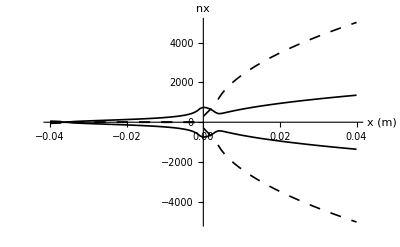

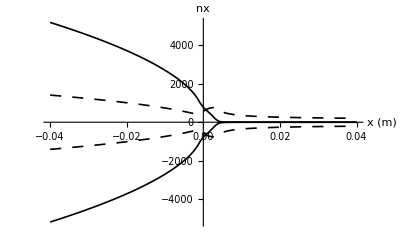

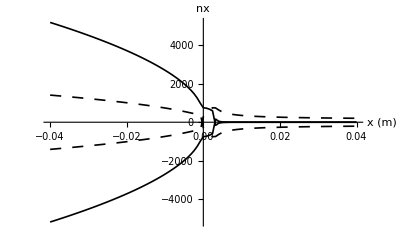

```mathematica
Show[{g7,g10},PlotRange->All,AxesOrigin->{0.,0.}]
Show[{g8,g11},PlotRange->All,AxesOrigin->{0.,0.}]
Show[{g9,g12},PlotRange->All,AxesOrigin->{0.,0.}]
```

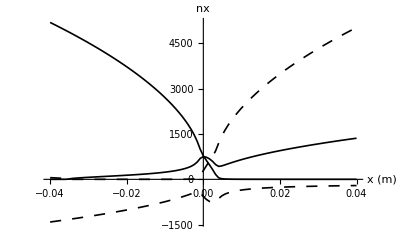

```mathematica
Show[{g8,g10},PlotRange->All,AxesOrigin->{0.,0.}]
```

Still both the 6th order and full Bessel solutions show the slow wave branch with a large imaginary part, and negative imaginary to boot. i.e. a growing wave.

Really looks about the same as with warm electrons

## Initialization

#### Magnetic field,Density and Temperature Profiles

```mathematica
bprof[x_]:=If[Abs[(BXmax-BXmin)/BXmax]>10^-6,BXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(BXmax-BXmin),BXmin];
```

```mathematica
nprof[x_]:=If[Abs[(nXmax-nXmin)/nXmax]>10^-6,nXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(nXmax-nXmin),nXmin];
```

```mathematica
tprof[x_]:=If[Abs[(TeXmax-TeXmin)/TeXmax]>10^-6,TeXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(TeXmax-TeXmin),TeXmin];
```